```mathematica
url="https://genealogy.math.ndsu.nodak.edu/id.php?id=";
```

```mathematica
Import[url<>ToString[145671],"Hyperlinks"]
```

{https://genealogy.math.ndsu.nodak.edu/index.php,https://genealogy.math.ndsu.nodak.edu/index.php,https://genealogy.math.ndsu.nodak.edu/search.php,https://genealogy.math.ndsu.nodak.edu/extrema.php,https://genealogy.math.ndsu.nodak.edu/about.php,https://genealogy.math.ndsu.nodak.edu/mission.php,http://www.ams.org/notices/200708/tx070801002p.pdf,https://epayment.ndus.nodak.edu/C22800_ustores/web/product_detail.jsp?PRODUCTID=2989&SINGLESTORE=true,https://genealogy.math.ndsu.nodak.edu/news.php,https://genealogy.math.ndsu.nodak.edu/staff.php,https://genealogy.math.ndsu.nodak.edu/recognition.php,https://genealogy.math.ndsu.nodak.edu/acknowledgments.php,https://genealogy.math.ndsu.nodak.edu/links.php,https://genealogy.math.ndsu.nodak.edu/faq.php,https://genealogy.math.ndsu.nodak.edu/posters.php,https://genealogy.math.ndsu.nodak.edu/submit.php,https://genealogy.math.ndsu.nodak.edu/contact.php,https://genealogy.math.ndsu.nodak.edu/mirrors.php,http://www.genealogy.math.ndsu.nodak.edu/,http://www.genealogy.ams.org/,http://www.math.uni-bielefeld.de/genealogy,http://genealogy.impa.br/,https://epayment.ndus.nodak.edu/C22800_ustores/web/product_detail.jsp?PRODUCTID=2989&SINGLESTORE=true,https://www.ndsu.edu/,https://www.ndsu.edu/math/,http://www.ams.org/,https://genealogy.math.ndsu.nodak.edu/id.php?id=145672,https://genealogy.math.ndsu.nodak.edu/submit-data.php?id=145671&edit=0,https://genealogy.math.ndsu.nodak.edu/submit-data.php?id=NEW&edit=0,https://genealogy.math.ndsu.nodak.edu/search.php,https://genealogy.math.ndsu.nodak.edu/about.php,https://genealogy.math.ndsu.nodak.edu/mission.php,https://genealogy.math.ndsu.nodak.edu/news.php,https://genealogy.math.ndsu.nodak.edu/staff.php,https://genealogy.math.ndsu.nodak.edu/recognition.php,https://genealogy.math.ndsu.nodak.edu/acknowledgments.php,https://genealogy.math.ndsu.nodak.edu/links.php,https://genealogy.math.ndsu.nodak.edu/faq.php,https://genealogy.math.ndsu.nodak.edu/posters.php,https://genealogy.math.ndsu.nodak.edu/submit.php,https://genealogy.math.ndsu.nodak.edu/contact.php,https://epayment.ndus.nodak.edu/C22800_ustores/web/product_detail.jsp?PRODUCTID=2989&SINGLESTORE=true}

```mathematica
Table[
hp=Import[url<>ToString[id],"Hyperlinks"];If[!MemberQ[hp,"https://genealogy.math.ndsu.nodak.edu/id.php?id="<>ToString[id]<>"&fChrono=1"],Missing[],id->ToExpression[#]&/@(Last/@(StringSplit[#,"="]&/@hp[[(Position[hp,"https://genealogy.math.ndsu.nodak.edu/id.php?id="<>ToString[id]<>"&fChrono=1"][[1,1]]+1);;-16]]))],{id,10}]
```

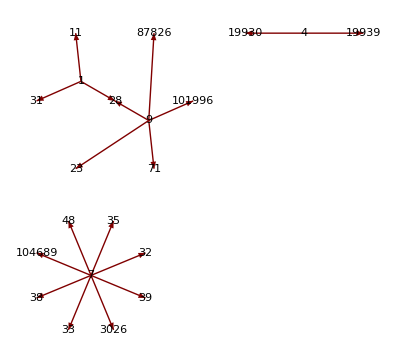

```mathematica
GraphPlot[Flatten@DeleteMissing[{{1->11,1->28,1->31},Missing[],Missing[],{4->19930,4->19939},Missing[],Missing[],{7->48,7->104689,7->38,7->33,7->3026,7->39,7->32,7->35},Missing[],{9->23,9->28,9->71,9->101996,9->87826},Missing[]}],VertexLabeling->True,DirectedEdges->True]
```